Values of Nodes

-Graphics-

Difference Between Nodes

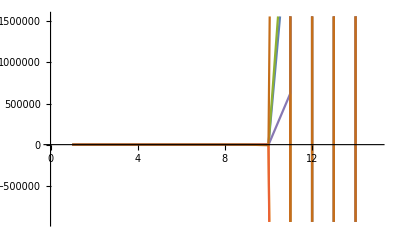

```mathematica
(*Time Delay Added In*)

(*Variables*)
h[X_]:=X^2-X(*4*X*(1-X)*); (*affects self*)
G[X_]:=X-X^2(*(1/4)*X*(X-1)*); (*affects others*)

(*initial values in the nodes*)
Node={0.2,0.7,0.21,0.71}; 

(*used in the update so when one node is changed, that doesn't affect other nodes currently being updated*)
NodeTemp = ConstantArray[0,Length[Node]];

(*1 means a time delay, 0 means regular*)
TimeDelay=
{{0,0,0,0},
{0,0,0,0},
{0,0,0,0},
{0,0,0,0}};

TimeDelayValue=Node;(*Holds values of the time delayed nodes*)

connect= (*strength of connections*)
{{0,1,0,0},
{1,0,1,0},
{0,1,0,1},
{0,0,1,0}};

(*Update this many times*)
IterationNum=15;  

(*keeps track of iteration info for graph*)

GraphVect=ConstantArray[0,{Length[Node],IterationNum }]; 

(*Used to update the Node Array*)
NodeUpdate= ConstantArray[0,{Length[Node]}];


(*Computations*)
For[io=1,io≤IterationNum,io++, (*io = iterations*)
For[jo=1,jo≤Length[Node],jo++, (*jo = self-node*)

(*set temp node to the first part of our model function*)
If[TimeDelay[[jo,jo]]==1,
NodeTemp[[jo]]=h[TimeDelayValue[[jo]]];TimeDelayValue[[jo]]=h[Node[[jo]]],
NodeTemp[[jo]]=h[Node[[jo]]];];

For[ko=1,ko≤Length[Node],ko++,(*ko = nodes affecting self-node*)

(*Add the connection values to the current self-node*)
If[TimeDelay[[jo,ko]]==1,
NodeTemp[[jo]]+=connect[[jo,ko]](G[Node[[jo]]]-G[TimeDelayValue[[ko]]]);TimeDelayValue[[ko]]=h[Node[[ko]]],
NodeTemp[[jo]]+=connect[[jo,ko]]*(G[Node[[jo]]]-G[Node[[ko]]]);]
];
];

For[jo=1,jo≤Length[Node],jo++,
GraphVect[[jo,io]]=Node[[jo]];
];
Node=NodeTemp;
];


(*Visuals*)
"Values of Nodes"
ListLinePlot[GraphVect]

num=0;
For[io=1,io≤Length[Node]-1,io++,
For[jo=io+1,jo≤Length[Node],jo++,
num++;
];
];

Synch = ConstantArray[0,{num,IterationNum}];
num=0;
For[io=1,io≤Length[Node]-1,io++,
For[jo=io+1,jo≤Length[Node],jo++,
num++;
Synch[[num]]=GraphVect[[io]]-GraphVect[[jo]]
];
];

"Difference Between Nodes"
ListLinePlot[Synch]
```